```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order+1,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];
];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];

{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];
If[order==1,
nnodes=4  ;
];
If[order==2,
nnodes=9;
];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
(*nnodes=Length[allcoords] order;*)
sz= Length[nnodes]2;
If[order==1,
rows=4  ;
];
If[order==2,
rows=9;
];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
(*{x1,x2}=nodes[[id1]];
{y1,y2}=nodes[[id2]];
If[Abs[x2-x1]<10^-3,
dir=2;
coord=nodes[[id1,2]];
,
dir=1;
coord=nodes[[id1,1]];

];
tol=10^-4;
radius=0.;

{els,ids}=ComputeBoundaryTopol[dir,coord,radius,nnodes,tol,order];*)

(*Print["els = ",els];
Print["ids = ",ids];*)
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

If[order==1,
kk=4;
];
If[order==2,
kk=9;
];

For[j=1,j≤kk,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
];

Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
GradPsi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.Transpose[GradPsi];

For[j=1,j≤kk,j++,

id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );

(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );

];

X[[i,1]]=x;
X[[i,2]]=y;

];



{sol,dsol,X}

]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear curvo*)
ContributeLineNewman[EF_,fx_,order_,vecnodes_,vecids_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];


x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;

If[Abs[(yf-y0)]<10^-6,
vertOrHor=1;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)

];
If[Abs[(xf-x0)]<10^-6,
vertOrHor=2;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)
];
If[vertOrHor==0,
Print["(*inclinado*)"];
Break[];
];

xx=Sum[shapes[[i]] co[[i]][[vertOrHor]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

Ef[[vecids[[i,1]] 2-1]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;
Ef[[ vecids[[i,3]] 2-1]]+=F3 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
Ef[[ vecids[[i,3]] 2]]+=F3 cos;

];

];

Ef

];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear curvo*)
ContributeLineNewmanCurverd[EF_,fx_,order_,vecnodes_,vecids_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];

If[order==1,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
co={co1,co2};
];
If[order==2,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
h2=Sqrt[(co[[3,1]]-co[[2,1]])^2 +(co[[3,2]]-co[[2,2]])^2];
co3=h1+h2;
co={co1,co2,co3};
];

xx=Sum[shapes[[i]] co[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin1;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin2;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos1;
Ef[[ vecids[[i,2]] 2]]+=F2 cos2;
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];


x3=coord[[3,1]];
y3=coord[[3,2]];
cos3=x3/Sqrt[x3 x3+y3 y3];
sin3=y3/Sqrt[x3 x3+y3 y3];

Ef[[vecids[[i,1]] 2-1]]+=F1 cos1 ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos2;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos3;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 sin1 ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin2;
Ef[[ vecids[[i,3]] 2]]+=F3 sin3;

];

];
Ef
];
```

```mathematica
(*Encontra os nos e a topologia de uma linha vertical ou horizontal*)
ComputeBoundaryTopol[XYorR_,linecoord_,radius_,nnodes_,tol_,order_]:=Block[{k,nodes,tabnodes,rangesearch,i0,j,elids,elnodes,xc,yc,i,a,newnodes,new,ids,vecids,h},

elids={};
elnodes={};
For[i=1,i≤Length[nnodes],i++,
xc=nnodes[[i,1]];
yc=nnodes[[i,2]];
If[XYorR==1,
If[Abs[(xc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==2,
If[Abs[(yc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==3,
h=Sqrt[(xc)^2 + (yc)^2.];
If[Abs[(h-radius)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

];
a=SortBy[Transpose[elnodes][[1]],Smaller];
newnodes={};
new={};
ids={};
vecids={};
If[XYorR==1||XYorR==2,
For[j=1,j≤Length[elnodes],j++,
AppendTo[new,elnodes[[j]]];
AppendTo[ids,elids[[j]]];
If[Length[new]==order+1,
AppendTo[newnodes,new];
AppendTo[vecids,ids];
new={new[[order+1]]};
ids={ids[[order+1]]};
];
];
,

nodes={};
newnodes={};
new={};
ids={};
For[j=1,j≤Length[a],j++,
For[k=1,k≤Length[elnodes],k++,
If[a[[j]]==elnodes[[k,1]],
AppendTo[nodes,{a[[j]],elnodes[[k,2]]}];
];
];
If[Length[nodes]==order+1,
AppendTo[newnodes,nodes];
nodes={nodes[[order+1]]};
];
];

i0=0;
Print["Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso! "];
rangesearch=h/30;
Print["rangesearch = ",rangesearch];

tabnodes=Table[{radius Cos[t],radius Sin[t]},{t,Pi/2,0,-Pi/2 1/(rangesearch 10)}];
ids={};
For[j=1,j≤Length[tabnodes],j++,
For[i=1,i≤Length[nnodes],i++,
(*Print["Abs[(tabnodes[[i]]-nnodes[[j]])] = ",Abs[(tabnodes[[i]]-nnodes[[j]])]];*)
If[Norm[(tabnodes[[j]]-nnodes[[i]])]≤rangesearch && i≠i0,
AppendTo[ids,i];
i0=i;
];
];
If[Length[ids]==order+1,
AppendTo[vecids,ids];
ids={ids[[order+1]]};
];
];

];
{newnodes,vecids}
]
```

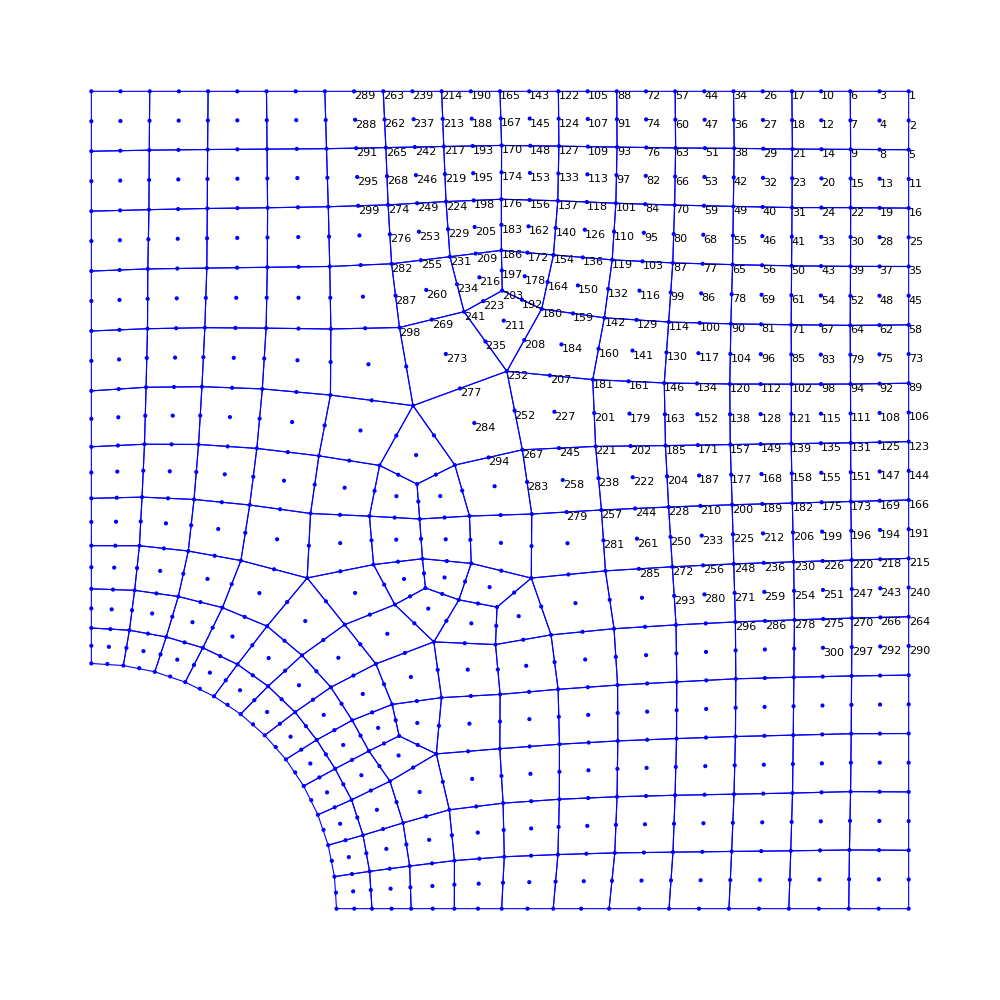

Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso!

rangesearch = 10.

5998.93

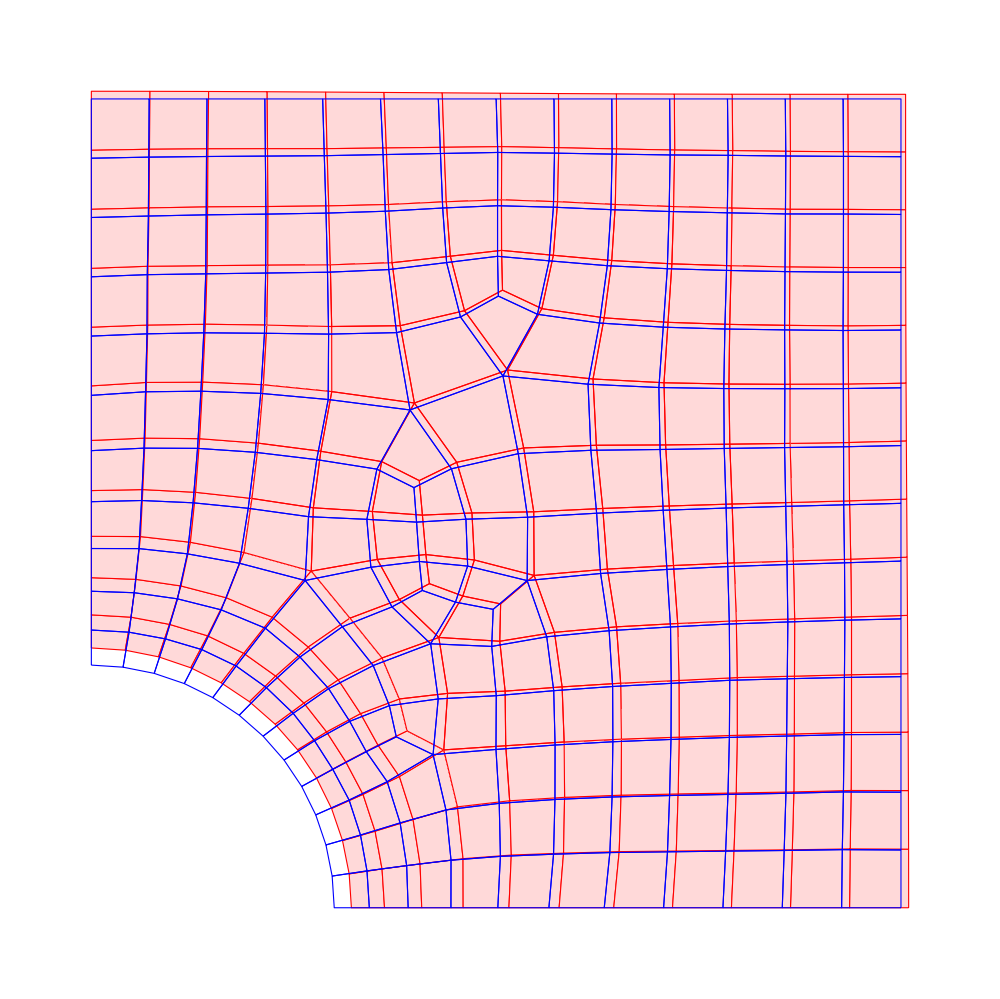

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elschapacomfuroleft.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\noschapacomfuroleft.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->1000]
order=2;
forcing=0.;
young=210000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,topol,order,forcing];
(*MatrixPlot[KE]*)
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,870,644,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,871,645,{{10^12,1},{1,1}},{0,0}];
tol=10^-4;
radius=300;
radiusdir=3;
coordy=0;(*naoprecisa*)
{newnodes,vecids}=ComputeBoundaryTopol[radiusdir,coordy,radius,nnodes,tol,order];
FE=Table[0,{Length[KE]}];
f[x_]:=10;
order=2;
FE=ContributeLineNewmanCurverd[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->1000]
```

```mathematica
(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),210000.,0.30][[1]]//Simplify//Chop;*)
```

```mathematica
(*sollists={};
sx=1;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 


stresslists={};
sx=1;
refine=0.5;

For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10 ,PlotRange->{-12,2}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] *)
```

10000.

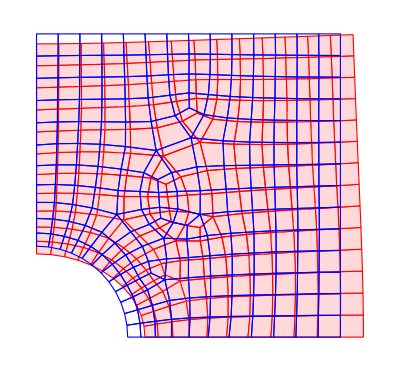

```mathematica
tol=10^-3;
radius=0;(*naoprecisa*)
xdir=1;
coordy=1000;
{newnodes,vecids}=ComputeBoundaryTopol[xdir,coordy,radius,nnodes,tol,order];
FE=Table[0,{Length[KE]}];
f[x_]:=10;
order=2;
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=1000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];

Show[meshVisDef,meshVis1,ImageSize->{1000}]
```

```mathematica
(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),210000.,0.30][[1]]//Simplify//Chop;*)
```

```mathematica
(*sollists={};
sx=1;
refine=1.;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 


stresslists={};
sx=1;


For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-5,40}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-18,12}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15 ,PlotRange->{-13,10}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] *)
```

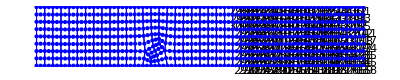

1474

-4.

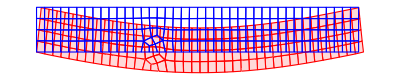

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\beamels.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\beamco.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->{1000}]
order=2;
forcing=0.;
young = 28 10^6(*KN/m2*);
nu=0.2;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,topol,order,forcing];
{KE,FE}=ApplyNodeBC[KE,FE,737,0,{{10^12,1},{1,10^16}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,58,0,{{1,1},{1,10^16}},{0,0}];
tol=10^-4;
radius=0.;
ydir=2;
coordy=0.2;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order];
f[x_]:=-x;
f[x_]:=-2;
diry=2;
Length[FE]
FE=Table[0,{1474}];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=4000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];

Show[meshVisDef,meshVis1,ImageSize->{1000}]
```

```mathematica
Min[sol]
Max[sol]
e = 28 10^6(*KN/m2*);
i=1 0.2 0.2 0.2/12;
Clear[x]
L=2.;
q=2.;
(*Sol=DSolve[{e i u''[x]==q L x/2 -q x x/2,u[0]==0,u[L]==0},u[x],x][[1,1,2]]/.{L->2,x->1}*)
Sol2=DSolve[{e i u''[x]== 0.667x-1/2x x x/3,u[0]==0,u[L]==0},u[x],x][[1,1,2]]/.{L->2,x->1}
```

-0.0000231906

7.561×10^-6

-0.0000111696

```mathematica
(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),e,0.2][[1]]//Simplify//Chop;
Clear[x,y,Sol];
sollists={};
sx=1;
refine=2;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}]

sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}]


stresslists={};
sx=1;


For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-151,151},ImageSize->{1000}]

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-7,7},ImageSize->{1000}]

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-30,30},ImageSize->{1000}]*)
```

-Graphics-

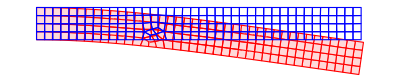

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\beamels.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\beamco.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->{1000}]
order=2;
forcing=0.;
young = 28 10^6(*KN/m2*);
nu=0.2;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,topol,order,forcing];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,737,729,{{10^12,1},{1,10^12}},{0,0}];
tol=10^-4;
radius=0.;
ydir=2;
coordy=0.2;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order];
f[x_]:=-x;
f[x_]:=-2;
diry=2;
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=1000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];

Show[meshVisDef,meshVis1,ImageSize->{1000}]
```

```mathematica
(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),e,0.2][[1]]//Simplify//Chop;*)
```

```mathematica
(*Clear[x,y,Sol];
sollists={};
sx=1;
refine=0.5;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}]

sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}]


stresslists={};
sx=1;


For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-655,655},ImageSize->{1000}]

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-109,109},ImageSize->{1000}]

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-83,13},ImageSize->{1000}]*)
```

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order]
```

{{{{0.,8.},{0.3125,8.},{0.625,8.}},{{0.625,8.},{0.9375,8.},{1.25,8.}},{{1.25,8.},{1.5625,8.},{1.875,8.}},{{1.875,8.},{2.1875,8.},{2.5,8.}},{{2.5,8.},{2.8125,8.},{3.125,8.}},{{3.125,8.},{3.4375,8.},{3.75,8.}},{{3.75,8.},{4.0625,8.},{4.375,8.}},{{4.375,8.},{4.6875,8.},{5.,8.}},{{5.,8.},{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.},{8.,8.}}},{{1,3,6},{6,12,18},{18,28,38},{38,51,66},{66,81,100},{100,119,142},{142,165,187},{187,206,227},{227,250,279},{279,317,391},{391,633,702},{702,729,754},{754,776,801}}}

```mathematica
Min[sol]
```

-0.000216218

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order]
```

{{{{0.,8.},{0.147059,8.},{0.294118,8.}},{{0.294118,8.},{0.441176,8.},{0.588235,8.}},{{0.588235,8.},{0.735294,8.},{0.882353,8.}},{{0.882353,8.},{1.02941,8.},{1.17647,8.}},{{1.17647,8.},{1.32353,8.},{1.47059,8.}},{{1.47059,8.},{1.61765,8.},{1.76471,8.}},{{1.76471,8.},{1.91176,8.},{2.05882,8.}},{{2.05882,8.},{2.20588,8.},{2.35294,8.}},{{2.35294,8.},{2.5,8.},{2.64706,8.}},{{2.64706,8.},{2.79412,8.},{2.94118,8.}},{{2.94118,8.},{3.08824,8.},{3.23529,8.}},{{3.23529,8.},{3.38235,8.},{3.52941,8.}},{{3.52941,8.},{3.67647,8.},{3.82353,8.}},{{3.82353,8.},{3.97059,8.},{4.11765,8.}},{{4.11765,8.},{4.26471,8.},{4.41176,8.}},{{4.41176,8.},{4.55882,8.},{4.70588,8.}},{{4.70588,8.},{4.85294,8.},{5.,8.}},{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}},{{1,3,6},{6,11,18},{18,27,36},{36,48,62},{62,77,94},{94,114,133},{133,154,178},{178,203,231},{231,257,287},{287,318,352},{352,386,420},{420,458,497},{497,540,581},{581,628,668},{668,705,737},{737,765,794},{794,824,858},{858,891,926},{926,960,1001},{1001,1049,1106},{1106,1174,1269},{1269,1450,1856},{1856,1988,2075},{2075,2140,2196},{2196,2246,2297},{2297,2339,2394},{2394,2445,2500}}}

```mathematica
Sum[FE[[i]],{i,1,Length[FE]}]
```

-600.

```mathematica
700/200.
```

3.5

```mathematica
Length[vecids]
```

6

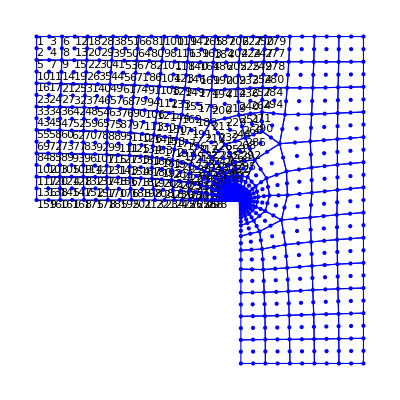

els = {{{0.,4.},{0.290438,4.}},{{0.290438,4.},{0.580877,4.}},{{0.580877,4.},{0.871315,4.}},{{0.871315,4.},{1.16175,4.}},{{1.16175,4.},{1.45219,4.}},{{1.45219,4.},{1.74263,4.}},{{1.74263,4.},{2.03307,4.}},{{2.03307,4.},{2.32351,4.}},{{2.32351,4.},{2.61087,4.}},{{2.61087,4.},{2.89823,4.}},{{2.89823,4.},{3.1333,4.}},{{3.1333,4.},{3.36837,4.}},{{3.36837,4.},{3.55713,4.}},{{3.55713,4.},{3.74589,4.}},{{3.74589,4.},{3.89519,4.}},{{3.89519,4.},{4.0445,4.}},{{4.0445,4.},{4.1612,4.}},{{4.1612,4.},{4.2779,4.}},{{4.2779,4.},{4.36827,4.}},{{4.36827,4.},{4.45864,4.}},{{4.45864,4.},{4.5281,4.}},{{4.5281,4.},{4.59757,4.}},{{4.59757,4.},{4.65067,4.}},{{4.65067,4.},{4.70377,4.}},{{4.70377,4.},{4.74419,4.}},{{4.74419,4.},{4.78461,4.}},{{4.78461,4.},{4.81527,4.}},{{4.81527,4.},{4.84593,4.}},{{4.84593,4.},{4.86913,4.}},{{4.86913,4.},{4.89233,4.}},{{4.89233,4.},{4.90986,4.}},{{4.90986,4.},{4.92738,4.}},{{4.92738,4.},{4.9406,4.}},{{4.9406,4.},{4.95382,4.}},{{4.95382,4.},{4.96377,4.}},{{4.96377,4.},{4.97373,4.}},{{4.97373,4.},{4.98123,4.}},{{4.98123,4.},{4.98872,4.}},{{4.98872,4.},{4.99436,4.}},{{4.99436,4.},{5.,4.}}}

ids = {159,160,161,168,175,178,185,195,201,213,221,234,242,255,265,276,288,298,308,320,334,344,355,368,383,396,407,416,429,439,453,462,474,482,497,509,522,528,537,541,547}

els = {{{5.,4.},{5.,3.99416}},{{5.,3.99416},{5.,3.98831}},{{5.,3.98831},{5.,3.97996}},{{5.,3.97996},{5.,3.97161}},{{5.,3.97161},{5.,3.95969}},{{5.,3.95969},{5.,3.94777}},{{5.,3.94777},{5.,3.93079}},{{5.,3.93079},{5.,3.9138}},{{5.,3.9138},{5.,3.88965}},{{5.,3.88965},{5.,3.8655}},{{5.,3.8655},{5.,3.83127}},{{5.,3.83127},{5.,3.79705}},{{5.,3.79705},{5.,3.74876}},{{5.,3.74876},{5.,3.70047}},{{5.,3.70047},{5.,3.63278}},{{5.,3.63278},{5.,3.56508}},{{5.,3.56508},{5.,3.47101}},{{5.,3.47101},{5.,3.37693}},{{5.,3.37693},{5.,3.24777}},{{5.,3.24777},{5.,3.11862}},{{5.,3.11862},{5.,2.94419}},{{5.,2.94419},{5.,2.76977}},{{5.,2.76977},{5.,2.53936}},{{5.,2.53936},{5.,2.30894}},{{5.,2.30894},{5.,2.02033}},{{5.,2.02033},{5.,1.73171}},{{5.,1.73171},{5.,1.44309}},{{5.,1.44309},{5.,1.15447}},{{5.,1.15447},{5.,0.865854}},{{5.,0.865854},{5.,0.577236}},{{5.,0.577236},{5.,0.288618}},{{5.,0.288618},{5.,0.}}}

ids = {547,553,560,568,576,586,594,607,614,622,628,640,649,659,668,677,685,693,704,713,721,733,743,756,768,789,805,822,838,852,864,878,893}

els = {{{5.,0.},{5.3,0.}},{{5.3,0.},{5.6,0.}},{{5.6,0.},{5.9,0.}},{{5.9,0.},{6.2,0.}},{{6.2,0.},{6.5,0.}},{{6.5,0.},{6.8,0.}},{{6.8,0.},{7.1,0.}},{{7.1,0.},{7.4,0.}},{{7.4,0.},{7.7,0.}},{{7.7,0.},{8.,0.}}}

ids = {893,898,907,915,922,928,933,937,940,942,943}

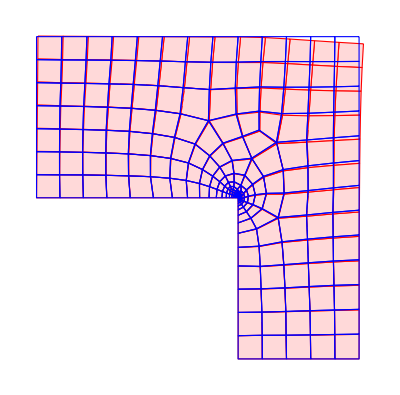

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\lshapeels.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\lshapenodes.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->{1000}]
order=2;
forcing=0.;
young =3 10^7(*KN/m2*);
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,topol,order,forcing];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,159,547,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,893,547,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,893,943,{{10^12,1},{1,10^12}},{0,0}];
(*tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order];*)
vecids={{227,250,279},{279,317,391},{391,633,702},{702,729,754},{754,776,801}};
newnodes={{{5.,8.},{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.},{8.,8.}}};
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];

Show[meshVisDef,meshVis1,ImageSize->{1000}]
```

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]]//Simplify//Chop;
```

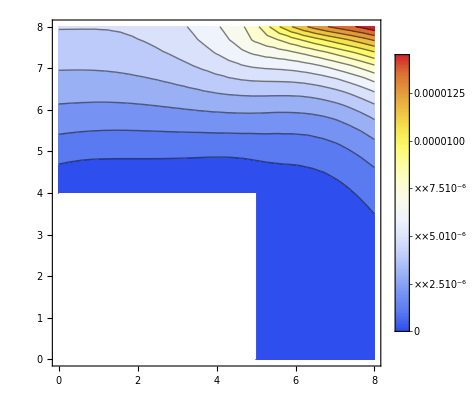

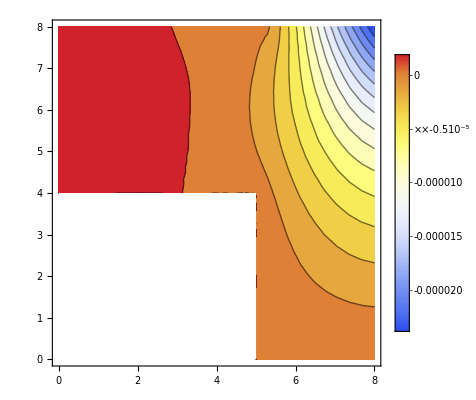

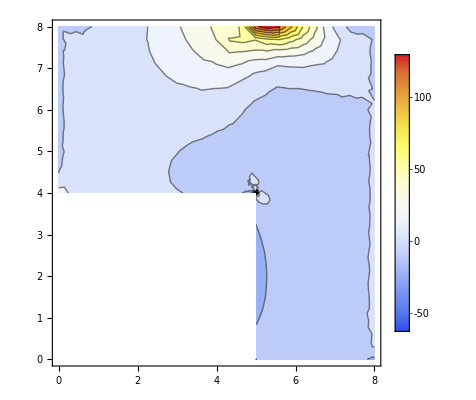

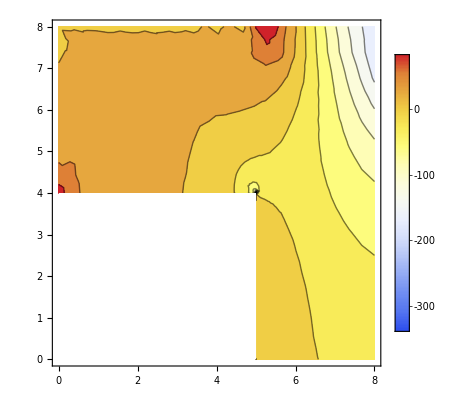

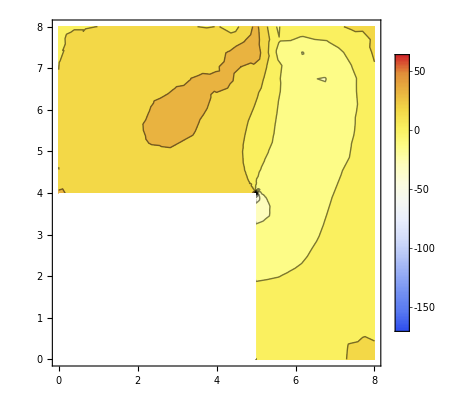

```mathematica
Clear[x,y,Sol];
sollists={};
sx=1;
refine=1;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]

stresslists={};
sx=1;


For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
```

```mathematica
Max[sol]
Min[sol]
```

0.0000238379

-0.000014516

```mathematica
Sum[FE[[i]],{i,1,Length[FE]}]
```

77.4124

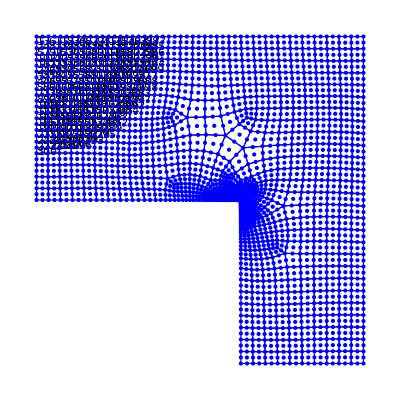

els = {{{0.,4.},{0.146846,4.}},{{0.146846,4.},{0.293692,4.}},{{0.293692,4.},{0.440538,4.}},{{0.440538,4.},{0.587384,4.}},{{0.587384,4.},{0.73423,4.}},{{0.73423,4.},{0.881076,4.}},{{0.881076,4.},{1.02792,4.}},{{1.02792,4.},{1.17477,4.}},{{1.17477,4.},{1.32161,4.}},{{1.32161,4.},{1.46846,4.}},{{1.46846,4.},{1.61531,4.}},{{1.61531,4.},{1.76215,4.}},{{1.76215,4.},{1.909,4.}},{{1.909,4.},{2.05584,4.}},{{2.05584,4.},{2.20269,4.}},{{2.20269,4.},{2.34954,4.}},{{2.34954,4.},{2.49638,4.}},{{2.49638,4.},{2.64323,4.}},{{2.64323,4.},{2.77897,4.}},{{2.77897,4.},{2.91471,4.}},{{2.91471,4.},{3.03738,4.}},{{3.03738,4.},{3.16005,4.}},{{3.16005,4.},{3.27038,4.}},{{3.27038,4.},{3.38071,4.}},{{3.38071,4.},{3.47952,4.}},{{3.47952,4.},{3.57833,4.}},{{3.57833,4.},{3.66649,4.}},{{3.66649,4.},{3.75465,4.}},{{3.75465,4.},{3.83304,4.}},{{3.83304,4.},{3.91143,4.}},{{3.91143,4.},{3.98092,4.}},{{3.98092,4.},{4.05041,4.}},{{4.05041,4.},{4.11185,4.}},{{4.11185,4.},{4.17329,4.}},{{4.17329,4.},{4.22749,4.}},{{4.22749,4.},{4.28168,4.}},{{4.28168,4.},{4.32938,4.}},{{4.32938,4.},{4.37707,4.}},{{4.37707,4.},{4.41898,4.}},{{4.41898,4.},{4.46088,4.}},{{4.46088,4.},{4.49764,4.}},{{4.49764,4.},{4.53439,4.}},{{4.53439,4.},{4.56659,4.}},{{4.56659,4.},{4.59878,4.}},{{4.59878,4.},{4.62694,4.}},{{4.62694,4.},{4.6551,4.}},{{4.6551,4.},{4.67971,4.}},{{4.67971,4.},{4.70432,4.}},{{4.70432,4.},{4.7258,4.}},{{4.7258,4.},{4.74728,4.}},{{4.74728,4.},{4.76601,4.}},{{4.76601,4.},{4.78475,4.}},{{4.78475,4.},{4.80108,4.}},{{4.80108,4.},{4.81741,4.}},{{4.81741,4.},{4.83163,4.}},{{4.83163,4.},{4.84586,4.}},{{4.84586,4.},{4.85824,4.}},{{4.85824,4.},{4.87062,4.}},{{4.87062,4.},{4.88139,4.}},{{4.88139,4.},{4.89217,4.}},{{4.89217,4.},{4.90153,4.}},{{4.90153,4.},{4.9109,4.}},{{4.9109,4.},{4.91905,4.}},{{4.91905,4.},{4.92719,4.}},{{4.92719,4.},{4.93427,4.}},{{4.93427,4.},{4.94135,4.}},{{4.94135,4.},{4.9475,4.}},{{4.9475,4.},{4.95365,4.}},{{4.95365,4.},{4.95899,4.}},{{4.95899,4.},{4.96434,4.}},{{4.96434,4.},{4.96897,4.}},{{4.96897,4.},{4.97361,4.}},{{4.97361,4.},{4.97764,4.}},{{4.97764,4.},{4.98167,4.}},{{4.98167,4.},{4.98517,4.}},{{4.98517,4.},{4.98866,4.}},{{4.98866,4.},{4.9917,4.}},{{4.9917,4.},{4.99473,4.}},{{4.99473,4.},{4.99737,4.}},{{4.99737,4.},{5.,4.}}}

ids = {637,638,641,643,652,658,662,675,683,692,704,717,730,741,756,770,784,798,815,832,846,864,881,897,913,928,944,958,974,988,1000,1017,1028,1046,1061,1074,1087,1100,1116,1130,1144,1159,1172,1183,1199,1212,1222,1233,1247,1260,1274,1285,1300,1311,1322,1333,1345,1353,1365,1377,1390,1402,1413,1426,1437,1453,1465,1477,1487,1498,1508,1520,1535,1550,1565,1579,1591,1604,1616,1625,1634}

els = {{{5.,4.},{5.,3.99732}},{{5.,3.99732},{5.,3.99463}},{{5.,3.99463},{5.,3.99143}},{{5.,3.99143},{5.,3.98822}},{{5.,3.98822},{5.,3.9844}},{{5.,3.9844},{5.,3.98057}},{{5.,3.98057},{5.,3.97601}},{{5.,3.97601},{5.,3.97144}},{{5.,3.97144},{5.,3.966}},{{5.,3.966},{5.,3.96055}},{{5.,3.96055},{5.,3.95406}},{{5.,3.95406},{5.,3.94756}},{{5.,3.94756},{5.,3.93982}},{{5.,3.93982},{5.,3.93208}},{{5.,3.93208},{5.,3.92286}},{{5.,3.92286},{5.,3.91363}},{{5.,3.91363},{5.,3.90265}},{{5.,3.90265},{5.,3.89167}},{{5.,3.89167},{5.,3.8786}},{{5.,3.8786},{5.,3.86553}},{{5.,3.86553},{5.,3.84999}},{{5.,3.84999},{5.,3.83446}},{{5.,3.83446},{5.,3.816}},{{5.,3.816},{5.,3.79755}},{{5.,3.79755},{5.,3.77566}},{{5.,3.77566},{5.,3.75376}},{{5.,3.75376},{5.,3.72783}},{{5.,3.72783},{5.,3.70189}},{{5.,3.70189},{5.,3.67121}},{{5.,3.67121},{5.,3.64053}},{{5.,3.64053},{5.,3.60431}},{{5.,3.60431},{5.,3.56809}},{{5.,3.56809},{5.,3.52543}},{{5.,3.52543},{5.,3.48276}},{{5.,3.48276},{5.,3.43263}},{{5.,3.43263},{5.,3.3825}},{{5.,3.3825},{5.,3.32379}},{{5.,3.32379},{5.,3.26507}},{{5.,3.26507},{5.,3.19653}},{{5.,3.19653},{5.,3.12799}},{{5.,3.12799},{5.,3.04833}},{{5.,3.04833},{5.,2.96867}},{{5.,2.96867},{5.,2.87651}},{{5.,2.87651},{5.,2.78435}},{{5.,2.78435},{5.,2.67834}},{{5.,2.67834},{5.,2.57232}},{{5.,2.57232},{5.,2.45113}},{{5.,2.45113},{5.,2.32994}},{{5.,2.32994},{5.,2.19241}},{{5.,2.19241},{5.,2.05489}},{{5.,2.05489},{5.,1.90811}},{{5.,1.90811},{5.,1.76133}},{{5.,1.76133},{5.,1.61456}},{{5.,1.61456},{5.,1.46778}},{{5.,1.46778},{5.,1.321}},{{5.,1.321},{5.,1.17422}},{{5.,1.17422},{5.,1.02744}},{{5.,1.02744},{5.,0.880666}},{{5.,0.880666},{5.,0.733889}},{{5.,0.733889},{5.,0.587111}},{{5.,0.587111},{5.,0.440333}},{{5.,0.440333},{5.,0.293555}},{{5.,0.293555},{5.,0.146778}},{{5.,0.146778},{5.,0.}}}

ids = {1634,1640,1645,1656,1662,1667,1676,1682,1689,1699,1710,1718,1727,1737,1747,1759,1777,1792,1808,1826,1841,1854,1868,1881,1898,1908,1922,1935,1947,1962,1979,1994,2013,2031,2044,2059,2077,2095,2113,2134,2156,2176,2194,2215,2235,2261,2285,2314,2347,2383,2422,2461,2495,2538,2572,2599,2630,2660,2690,2716,2741,2766,2791,2816,2843}

els = {{{5.,0.},{5.15,0.}},{{5.15,0.},{5.3,0.}},{{5.3,0.},{5.45,0.}},{{5.45,0.},{5.6,0.}},{{5.6,0.},{5.75,0.}},{{5.75,0.},{5.9,0.}},{{5.9,0.},{6.05,0.}},{{6.05,0.},{6.2,0.}},{{6.2,0.},{6.35,0.}},{{6.35,0.},{6.5,0.}},{{6.5,0.},{6.65,0.}},{{6.65,0.},{6.8,0.}},{{6.8,0.},{6.95,0.}},{{6.95,0.},{7.1,0.}},{{7.1,0.},{7.25,0.}},{{7.25,0.},{7.4,0.}},{{7.4,0.},{7.55,0.}},{{7.55,0.},{7.7,0.}},{{7.7,0.},{7.85,0.}},{{7.85,0.},{8.,0.}}}

ids = {2843,2857,2875,2890,2906,2919,2929,2943,2956,2968,2979,2989,2998,3006,3013,3019,3024,3028,3031,3033,3035}

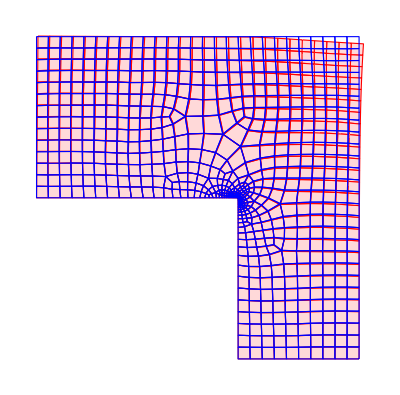

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\lshapeels2.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\lshapenodes2.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->{1000}]
order=2;
forcing=0.;
young =3 10^7(*KN/m2*);
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,topol,order,forcing];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,637,1634,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2843,1634,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2843,3035,{{10^12,1},{1,10^12}},{0,0}];
(*tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,order];*)
vecids={{858,891,926},{926,960,1001},{1001,1049,1106},{1106,1174,1269},{1269,1450,1856},{1856,1988,2075},{2075,2140,2196},{2196,2246,2297},{2297,2339,2394},{2394,2445,2500}};
newnodes={{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}};
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];

Show[meshVisDef,meshVis1,ImageSize->{1000}]
```

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]]//Simplify//Chop;
```

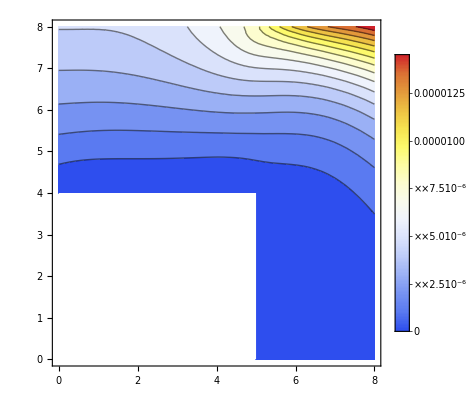

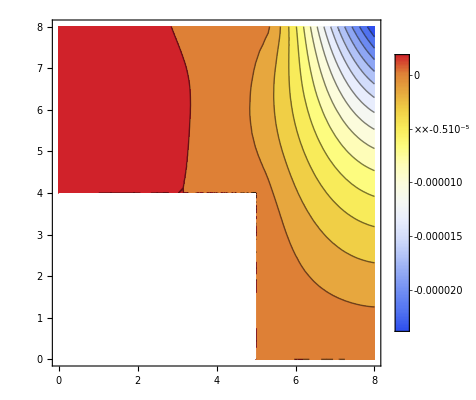

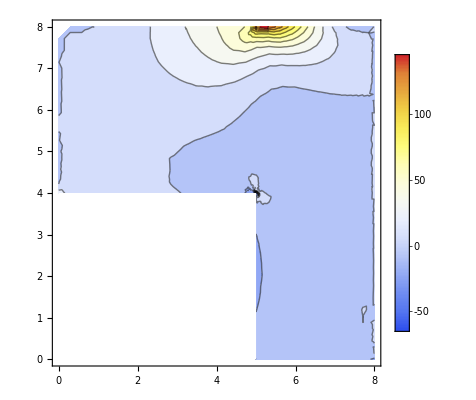

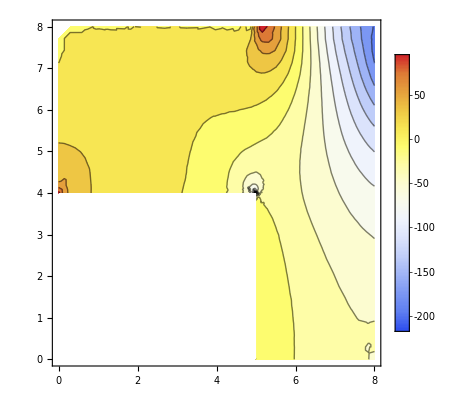

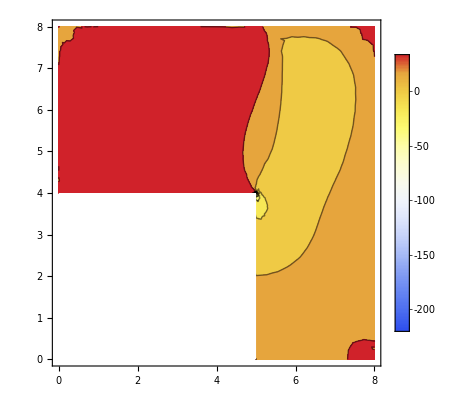

```mathematica
Clear[x,y,Sol];
sollists={};
sx=1;
refine=1;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]

stresslists={};
sx=1;


For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->{1000}];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
```

```mathematica
Max[sol]
Min[sol]
```

0.000014516

-0.0000238379

```mathematica
Length[KE]
```

6070